```mathematica
d = 1.;
Cth = 1.;
a = 1.;

nTerms = 1500;
sepMultMin = 0.5;
sepMultMax = 1500;
nSep = 200;
sepMults =sepMultMin Table[(sepMultMax/sepMultMin)^((i-1)/(nSep-1)),{i,1,nSep}];
seps =sepMults d Cth/a;

vMFs = 2 Sqrt[(d a)/(seps Cth)];
gammaScales = Sqrt[a/(d seps Cth)];
```

```mathematica
nGamma = 100;
gMin = 1. gammaScales;
gMax = gammaScales (7.Sqrt[sepMults/200]+1);
vGuess = vMFs (3.5Sqrt[sepMults/200]+1);
gammaVals =Table[Subdivide[gMin[[i]], gMax[[i]], nGamma-1],{i,1,Length[sepMults]}];

waveSpeeds = Table[Table[FindRoot[2 Cth Sqrt[d gammaVals[[j,i]] vee]==1+1/(Exp[seps[[j]] gammaVals[[j,i]]+seps[[j]] Sqrt[gammaVals[[j,i]]vee/d]]-1)+1/(Exp[-seps[[j]] gammaVals[[j,i]]+seps[[j]] Sqrt[gammaVals[[j,i]]vee/d]]-1),{vee,vGuess[[j]]}][[1,2]],{i,1,nGamma}],{j,1,Length[seps]}];

minSpeeds = Table[Min[waveSpeeds[[i]]],{i,1,Length[seps]}];
minSpeedMults = minSpeeds/vMFs;

minSpeedLocs = Flatten[Table[Position[waveSpeeds[[i]],minSpeeds[[i]]],{i,1,Length[waveSpeeds]}]];
minGammas = Table[gammaVals[[i,minSpeedLocs[[i]]]],{i,1,Length[minSpeedLocs]}];

waveSpeedsHeavi = Table[FindRoot[Cth==seps[[j]]/(2d)Sum[((4 i d)/(Pi vee seps[[j]]))^(1/2)Exp[-(i vee seps[[j]])/(4 d)]-i Erfc[((i vee seps[[j]])/(4 d))^(1/2)],{i,1,nTerms}],{vee,vMFs[[j]]}][[1,2]],{j,1,Length[seps]}];
waveSpeedMultsHeavi = waveSpeedsHeavi/(vMFs/2);
```

General::munfl: 1/(9.80495×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.79945×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.74453×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-717.123] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.645] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.167] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

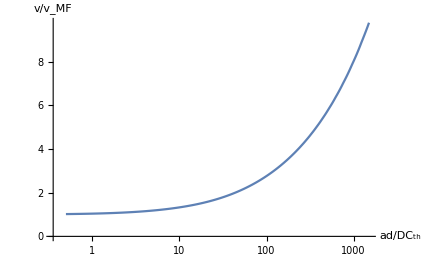

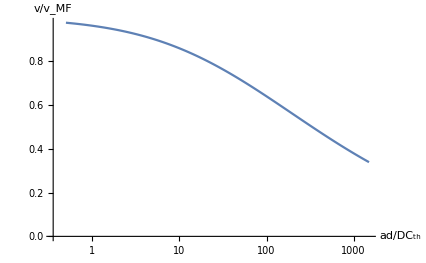

```mathematica
ListLogLinearPlot[Transpose[{sepMults,minSpeedMults}],Joined->True,AxesLabel->{"ad/DC_th","v/v_MF"},PlotRange->All]
ListLogLinearPlot[Transpose[{sepMults,waveSpeedMultsHeavi}],Joined->True,AxesLabel->{"ad/DC_th","v/v_MF"},PlotRange->All]
```

```mathematica
num = 100.;
func1 = Interpolation[Transpose[{sepMults,minSpeedMults}],InterpolationOrder->1];
funcInf = Interpolation[Transpose[{sepMults,waveSpeedMultsHeavi}],InterpolationOrder->1];
func1[num]
funcInf[num]
```

2.76245

0.639402

```mathematica
numericsSepMults = {1.,3.,10.,30.,100.,300.,1000.};

numericsHill = {1.,1.5,2.,3.,5.};
numericsWaveSpeedMults = {{1.0054150301125955,1.0822671953179088,1.2946131659976388,1.73371669568575,2.729704301075269,5,5},{1.0138702903767698,1.0581567670879009,1.1366860465116269,1.2431853195977993,1.2710513245033128,1.1326646882798055,0.8908991228070179},{1.0044036235530942,1.046263157894737,1.1029574892624032,1.1474717973635278,1.088146551724138,0.9267822736030822,0.7039625850340125},{1.0081064134718742,1.0386057092051013,1.0632225654365148,1.045977011494253,0.9324473684210528,0.7658244680851064,0.5756602112676056},{1.0049999999999997,1.0220588235294117,1.0105958587500252,0.9437707562591421,0.8097463401750676,0.6562459005896906,0.5021335891812867}};
```

```mathematica
plotColors = {RGBColor[0.5, 0.5, 1.],RGBColor[1., 0.5, 0.5],RGBColor[0.5,0.5,0.5],RGBColor[1., 0.8, 0.4],RGBColor[0.4, 0.8, 0.4]};

wid = 2800;
hei = 2600;
aR = hei/wid;
minorThickness = Thickness[20/wid];
majorThickness = Thickness[25/wid];
majorMajorThickness = Thickness[30/wid];
tL = 75/wid;
fS = Directive[Black,minorThickness];
tS = Directive[Black,minorThickness];
markerSize = wid/18;
markerPrefs = Table[Graphics[{plotColors[[i]],Thickness[0.15],Circle[]}, ImageSize->markerSize],{i,1,5}];

pR = {{0.7,1300},{0,3.}};
pR2 = {{0.7,1300},{0,2.}};
fT = {{{#,"",{tL,0}}&/@{1,2},None},{{#,"",{tL,0}}&/@{1,10,100,1000},None}};
fT2 = {{{#,"",{tL,0}}&/@{1,2},None},{{#,"",{tL,0}}&/@{1,30,1000},None}};
```

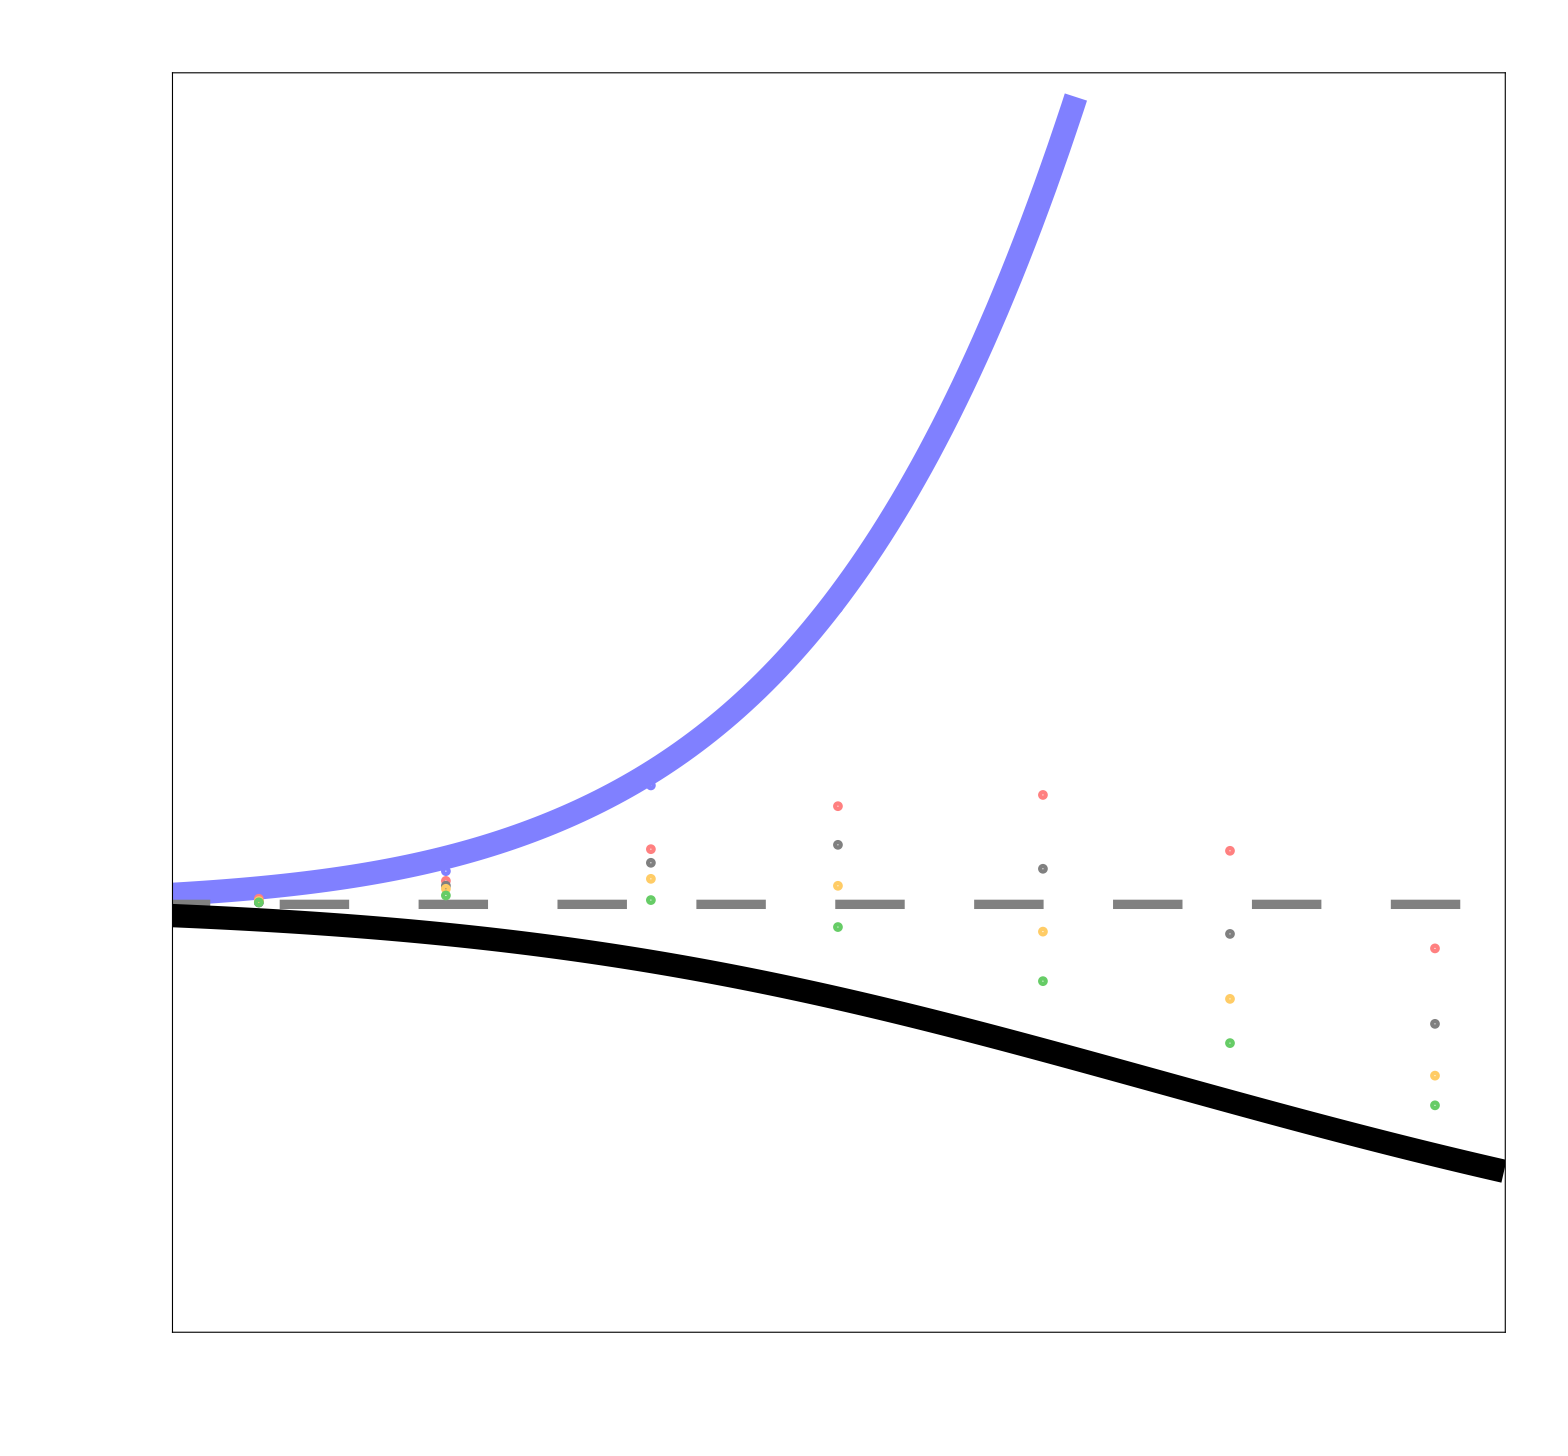

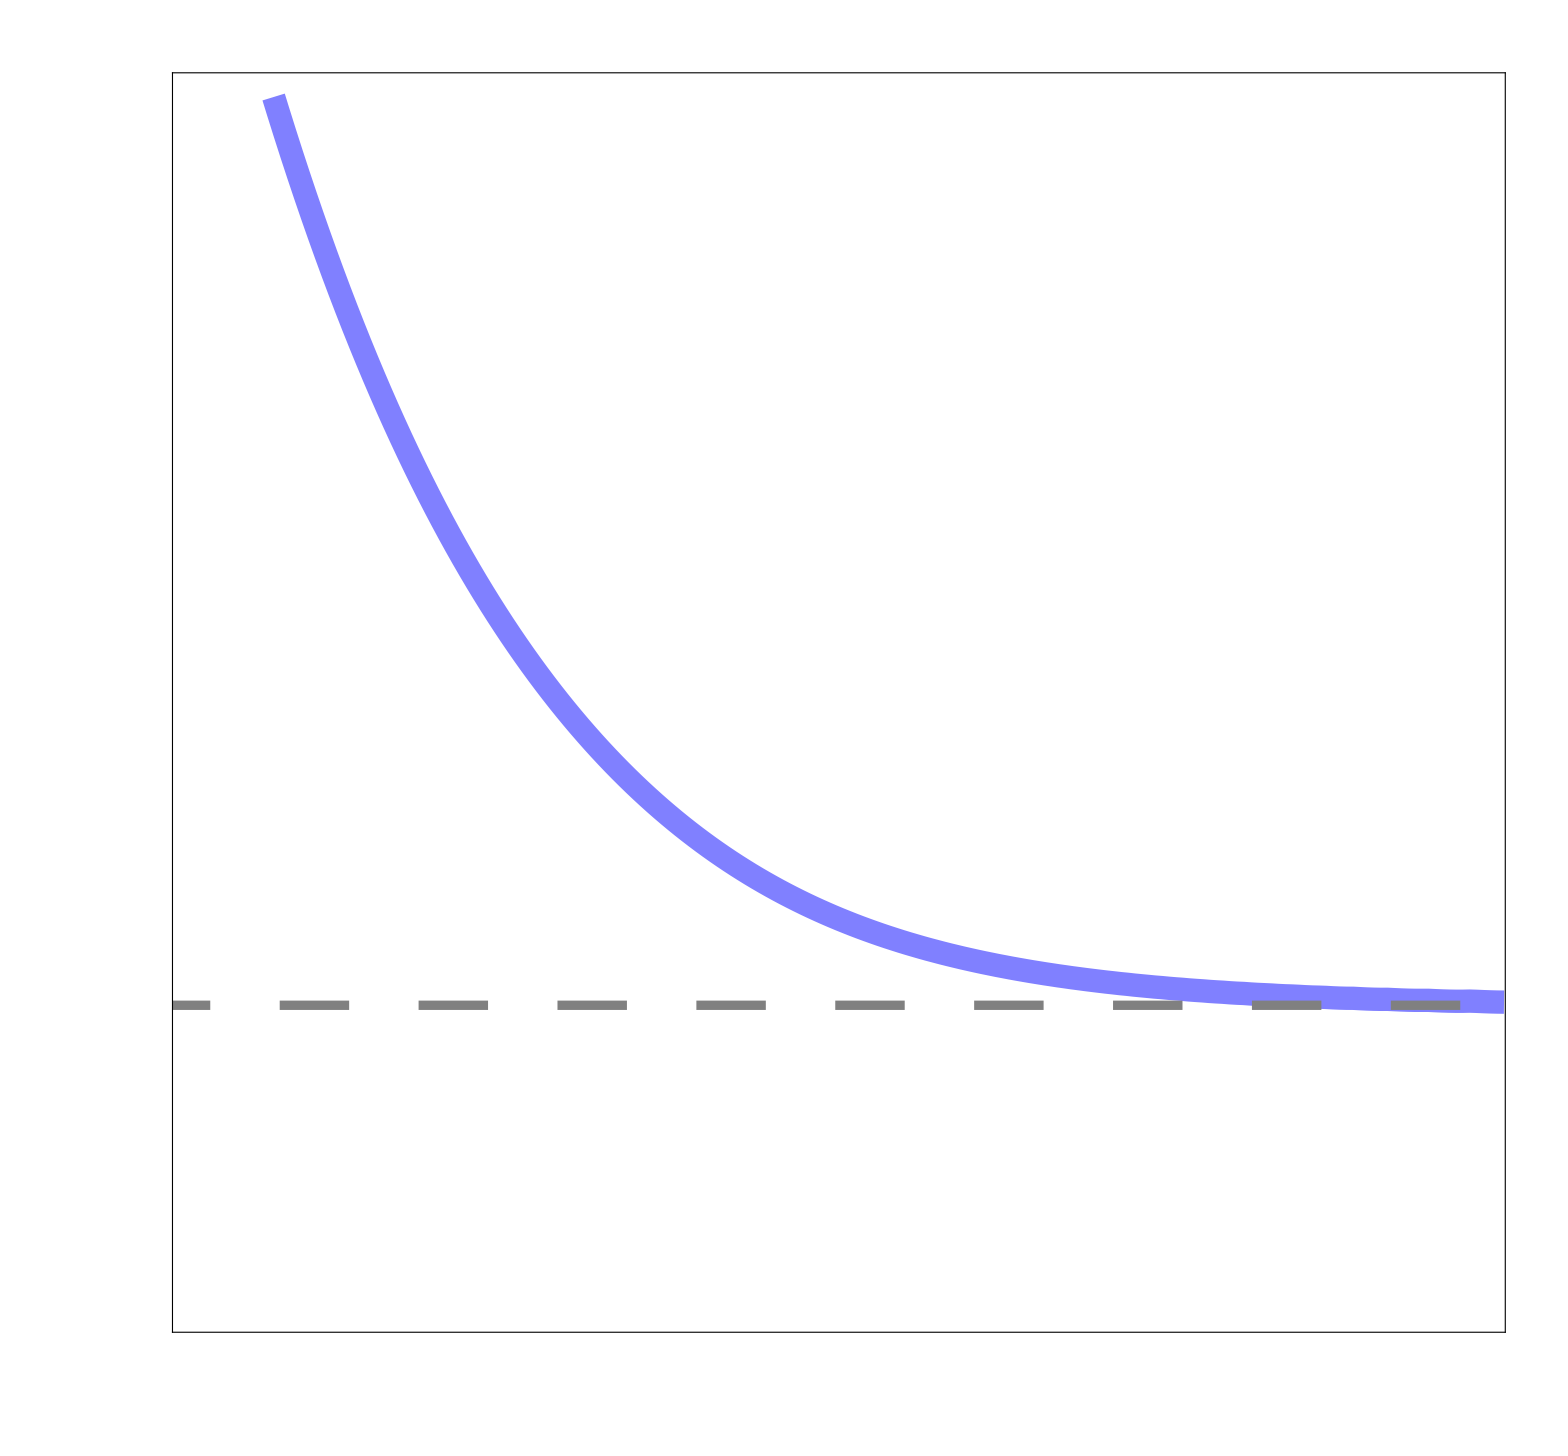

```mathematica
waveSpeedMultPlot = Show[ListLogLinearPlot[Transpose[{sepMults,minSpeedMults}],Joined->True,PlotStyle->{plotColors[[1]],majorMajorThickness},AspectRatio->aR,PlotRange->pR,Frame->True,FrameStyle->fS,FrameTicks->fT, FrameTicksStyle->tS],ListLogLinearPlot[Transpose[{sepMults,0.sepMults+1}],Joined->True,PlotStyle->{Gray,Dashing[{0.04,0.04}],Thickness[12/wid]}],ListLogLinearPlot[Transpose[{sepMults,waveSpeedMultsHeavi}],Joined->True,PlotStyle->{Black,majorMajorThickness}],Table[ListLogLinearPlot[Transpose[{numericsSepMults,numericsWaveSpeedMults[[i]]}],PlotMarkers->markerPrefs[[i]]],{i,1,5}],ImageSize->wid]

waveSpeedPlot = Show[ListLogLinearPlot[Transpose[{sepMults,minSpeeds}],Joined->True,PlotStyle->{plotColors[[1]],majorMajorThickness},AspectRatio->aR,PlotRange->pR2,Frame->True,FrameStyle->fS,FrameTicks->fT2, FrameTicksStyle->tS],ListLogLinearPlot[Transpose[{sepMults,0.sepMults+0.5}],Joined->True,PlotStyle->{Gray,Dashing[{0.04,0.04}],Thickness[12/wid]}],ImageSize->wid]
```

```mathematica
Export["waveSpeedMultPlot.pdf",waveSpeedMultPlot]
```

waveSpeedMultPlot.pdf

```mathematica
Export["waveSpeedPlot.pdf",waveSpeedPlot]
```

waveSpeedPlot.pdf

```mathematica
indMin = -10;
indMax = 10;
```

```mathematica
plotSeps = {1,30,1000};
waveSpeedsHeaviFunc = Interpolation[Transpose[{seps,waveSpeedsHeavi}],InterpolationOrder->1];
minSpeedsFunc = Interpolation[Transpose[{seps,minSpeeds}],InterpolationOrder->1];
minGammasFunc = Interpolation[Transpose[{seps,minGammas}],InterpolationOrder->1];

plotWaveSpeedsHeavi = waveSpeedsHeaviFunc[plotSeps];
plotMinSpeeds = minSpeedsFunc[plotSeps];
plotMinGammas = minGammasFunc[plotSeps];
```

```mathematica
concHeavi = Table[Table[HeavisideTheta[-0.5-j](((-4 j d)/(Pi plotWaveSpeedsHeavi[[i]] plotSeps[[i]]))^(1/2)Exp[(j plotWaveSpeedsHeavi[[i]] plotSeps[[i]])/(4 d)]+j Erfc[(-(j plotWaveSpeedsHeavi[[i]] plotSeps[[i]])/(4 d))^(1/2)]),{j,indMin,indMax}],{i,1,Length[plotSeps]}];
concHeavi = Re[(#/Max[#])&/@concHeavi];

concN1 = Re[Table[Table[Exp[-plotSeps[[i]](j plotMinGammas[[i]]+Abs[j]Sqrt[plotMinGammas[[i]]plotMinSpeeds[[i]]/d])],{j,indMin,indMax}],{i,1,Length[plotSeps]}]];
```

General::munfl: Exp[-998.176] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1996.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2994.53] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
wid = 1200;
hei = 833;
aR = hei/wid;
minorThickness = Thickness[15/wid];
majorThickness = Thickness[20/wid];
majorMajorThickness = Thickness[30/wid];
tL = 45/wid;
fS = Directive[Black,minorThickness];
tS = Directive[Black,minorThickness];
markerSize = wid/10;
markerPrefsHeavi = Graphics[{Black,Thickness[0.15],Circle[]}, ImageSize->60];
markerPrefsN1 = Graphics[{plotColors[[1]],Thickness[0.15],Circle[]}, ImageSize->60];

pR = {{-10,10},{0,1}};
fT = {{{#,"",{tL,0}}&/@{},None},{{#,"",{tL,0}}&/@{},None}};
```

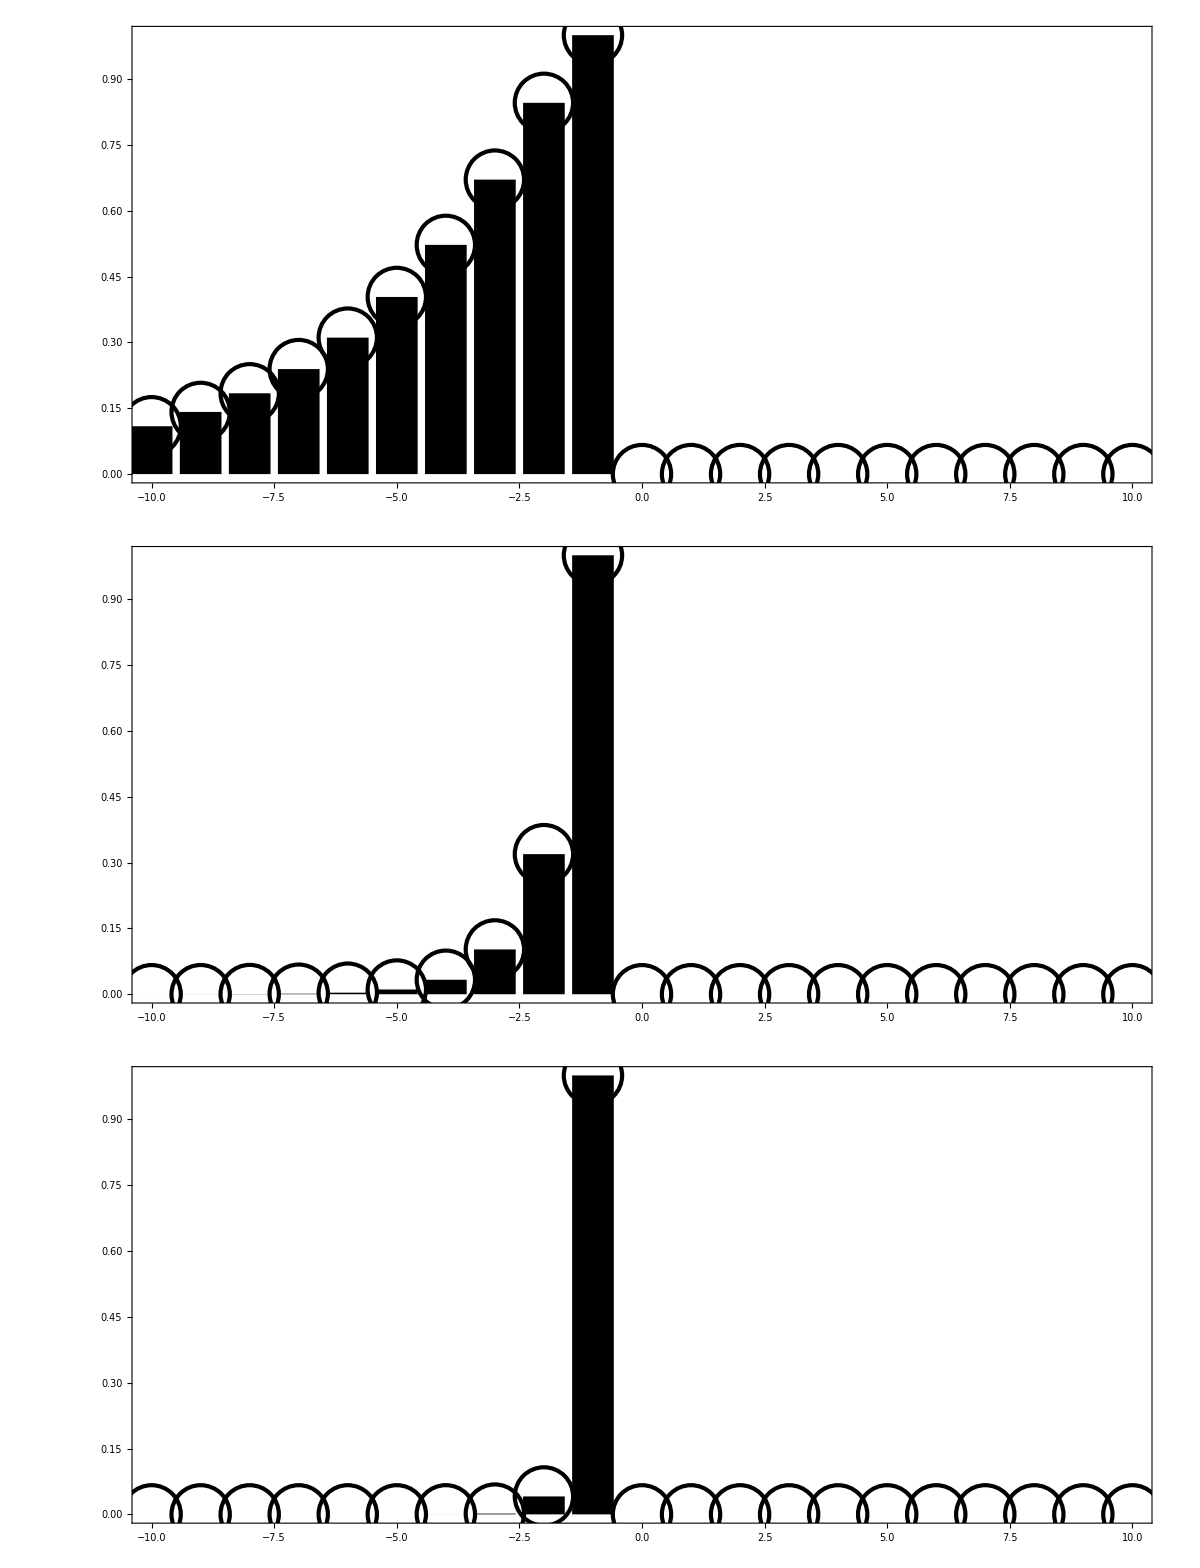

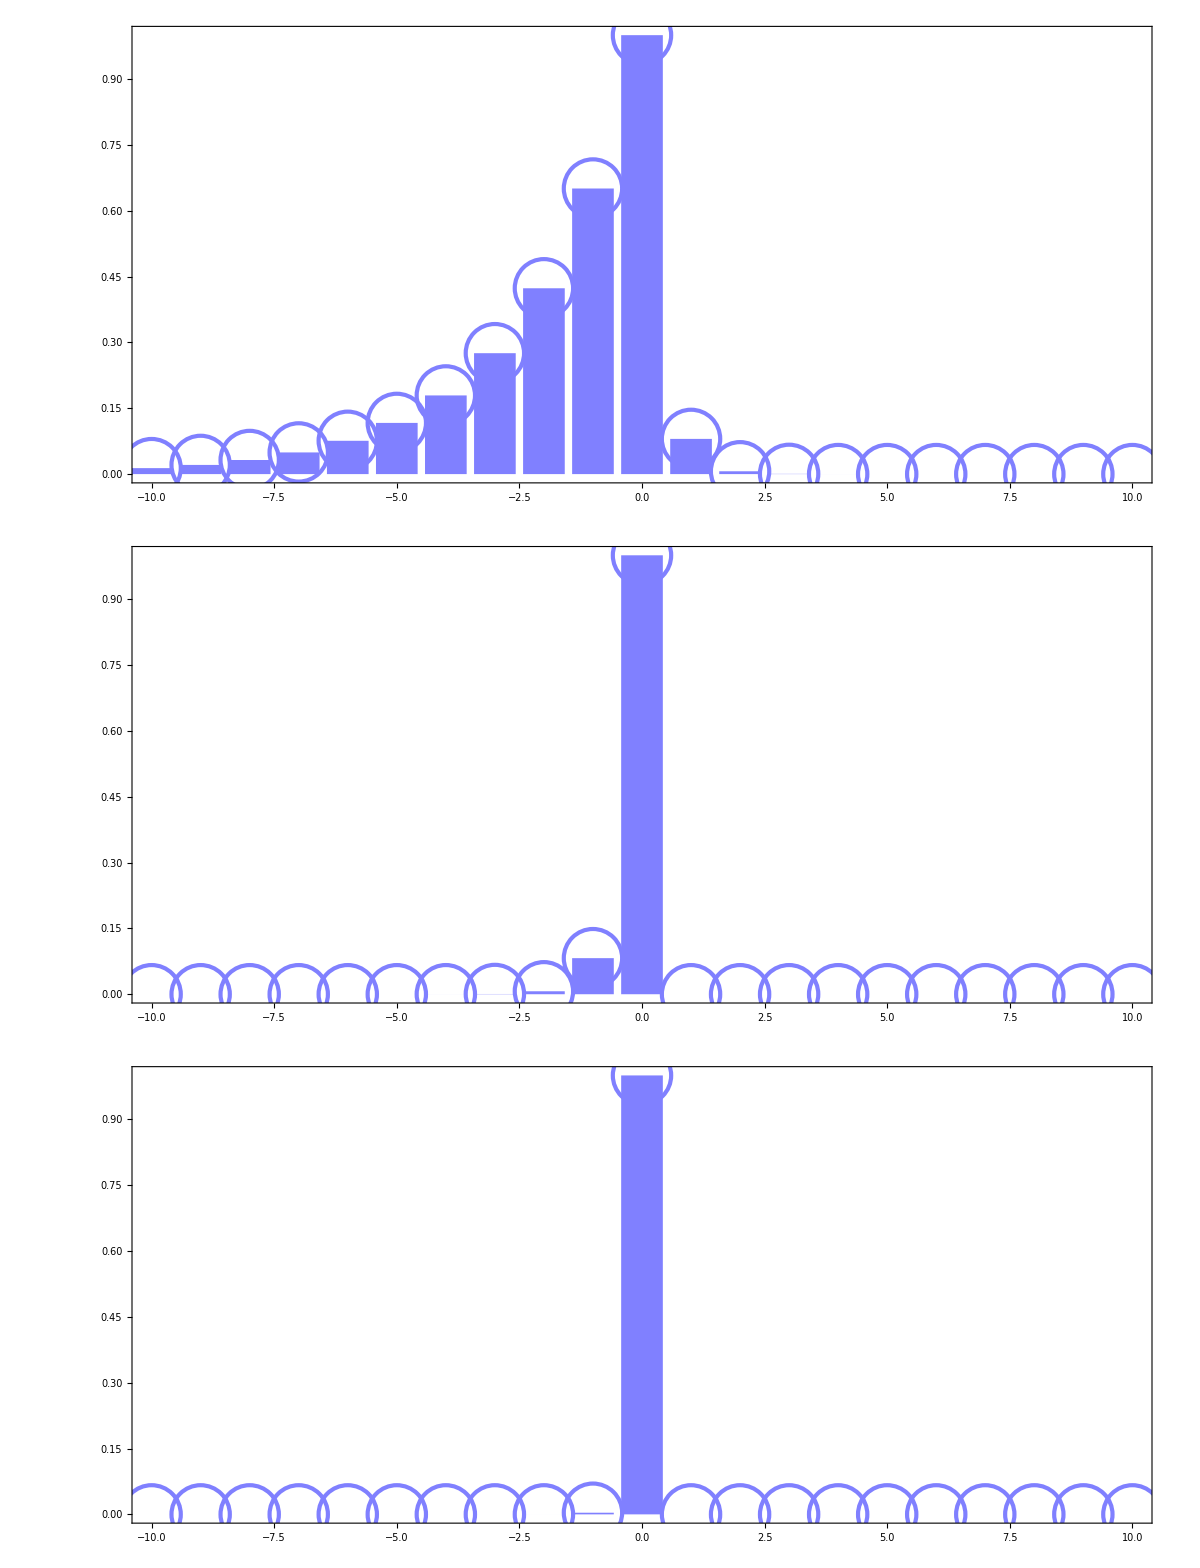

```mathematica
heavisideConcPlots = GraphicsColumn[Table[ListPlot[Transpose[{Table[i,{i,indMin,indMax}],concHeavi[[i]]}],Filling->Axis,FillingStyle->Directive[Black,majorMajorThickness],PlotMarkers->markerPrefsHeavi,PlotRange->pR,Frame->True,FrameStyle->fS,FrameTicks->fT,AspectRatio->aR,ImageSize->wid],{i,1,Length[plotSeps]}],Spacings->-12,ImageSize->wid]

n1ConcPlots = GraphicsColumn[Table[ListPlot[Transpose[{Table[i,{i,indMin,indMax}],concN1[[i]]}],Filling->Axis,FillingStyle->Directive[plotColors[[1]],majorMajorThickness],PlotMarkers->markerPrefsN1,PlotRange->pR,Frame->True,FrameStyle->fS,FrameTicks->fT,AspectRatio->aR,ImageSize->wid],{i,1,Length[plotSeps]}],Spacings->-12,ImageSize->wid]
```

```mathematica
Export["heavisideConcPlots.pdf",heavisideConcPlots]
Export["n1ConcPlots.pdf",n1ConcPlots]
```

heavisideConcPlots.pdf

n1ConcPlots.pdf